```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
```

/home/zack/oscillators/faraday

Single run plots

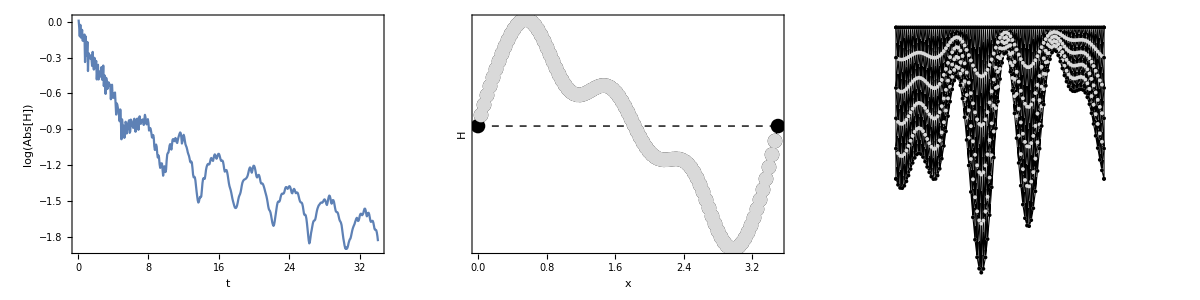

22.000000 0.800000

```mathematica
filebase="data/random191";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
Grid[{{ListPlot[Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}],Joined->True,PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{{0,0},{length,0}}},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]],Directive[Black,Dashed,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{SortBy[{#[[1]],#[[2]]-height}&/@mesh2[[top]],First],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]}}]
lst[[-1]]
```

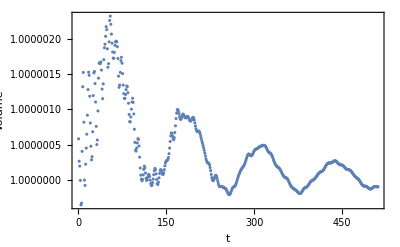

```mathematica
(* Numerical loss of fluid volume during saturation, but not too bad...*)
ListPlot[Total[#[[top,2]]]/(Length[top]*height)&/@mesh,Axes->False,Frame->True,FrameLabel->{t,"Volume"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]]]
```

```mathematica
modes=Table[Pi*n/length,{n,1,20}]
frequencies=2*(980*modes*Tanh[height*modes]*(1+72/980*modes^2))^(1/2)/(2*Pi)
modes2=Table[Pi*n/length,{n,1,20}]
frequencies2=2*(980*modes2*Tanh[height*modes2]*(1+72/980*modes2^2))^(1/2)/(2*Pi)
```

{0.897598,1.7952,2.69279,3.59039,4.48799,5.38559,6.28319,7.18078,8.07838,8.97598,9.87358,10.7712,11.6688,12.5664,13.464,14.3616,15.2592,16.1568,17.0544,17.952}

{6.30357,12.5561,18.9171,25.6296,32.8713,40.7312,49.2379,58.3864,68.1559,78.52,89.4511,100.923,112.912,125.396,138.356,151.773,165.634,179.922,194.626,209.733}

{0.897598,1.7952,2.69279,3.59039,4.48799,5.38559,6.28319,7.18078,8.07838,8.97598,9.87358,10.7712,11.6688,12.5664,13.464,14.3616,15.2592,16.1568,17.0544,17.952}

{6.30357,12.5561,18.9171,25.6296,32.8713,40.7312,49.2379,58.3864,68.1559,78.52,89.4511,100.923,112.912,125.396,138.356,151.773,165.634,179.922,194.626,209.733}

Generate box substrate

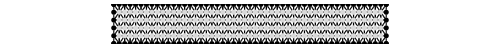

```mathematica
filebase="data/flat";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(Max[mesh[[All,All,2]]]-Min[mesh[[All,All,2]]])/(length+2),PlotRange->{{-1,length+1},{Min[mesh[[All,All,2]]],Max[mesh[[All,All,2]]]}}]
```

```mathematica
modes=ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate modes"][[1]]+1]]]];
smodes=Length[modes]/2;
subss=ConstantArray[0.,{smodes,smodes}]
subsc=Normal[SparseArray[Table[{i,1}->modes[[i]],{i,1,smodes}],{smodes,smodes}]]
subcs=ConstantArray[0.,{smodes,smodes}]
subcc=Normal[SparseArray[Table[{i,1}->modes[[smodes+i]],{i,1,smodes}],{smodes,smodes}]]
file=OpenWrite["data/boxsubstrate.dat"]
WriteString[file,smodes]
WriteString[file,"\n"]
Do[Do[WriteString[file,subss[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subsc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcs[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Do[Do[WriteString[file,subcc[[j,i]]]; WriteString[file," "];,{i,1,smodes}];WriteString[file,"\n"],{j,1,smodes}]
WriteString[file,"\n"];
Close[file]
```

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

{{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.}}

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

OutputStream[…]

data/boxsubstrate.dat

Animation

```mathematica
m0=Length[mesh]-500;
m1=Length[mesh];
If[!DirectoryQ["rectangleanimation"],CreateDirectory["rectangleanimation"]];
Monitor[Do[
acc=ToExpression[StringSplit[lst[[-1]]," "]][[2]];
freq=ToExpression[StringSplit[lst[[-1]]," "]][[1]];
amp=980*acc/(2*Pi*freq)^2;
z0=amp*Sin[2*Pi*m/15];
mesh2={#[[1]],z0+#[[2]]}&/@mesh[[m]];
p=Grid[{{ListPlot[{Transpose[{Range[Length[norms]]/15,Log[norms]/Log[10]}],Transpose[{Range[m]/15,Log[norms[[1;;m]]]/Log[10]}]},Joined->True,PlotStyle->{Directive[AbsoluteThickness[1],LightGray],Directive[AbsoluteThickness[2],Black]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{t,Log[Abs[H]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],Show[ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]]},FrameTicks->{Automatic,None},Joined->True,PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[1]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]],ListPlot[{{#[[1]],#[[2]]-height}&/@mesh2[[top]],{#[[1]],#[[2]]-height}&/@mesh2[[top2]]},FrameTicks->None,Joined->False,PlotStyle->{Directive[Black,PointSize[0.03]],Directive[LightGray,PointSize[0.03]]},PlotRange->All,ImageSize->350,ImagePadding->{{75,15},{75,15}},AspectRatio->1,Axes->False,Frame->True,FrameLabel->{x,H},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2.0]]]],
ListPlot[{mesh2,mesh2[[top]],mesh2[[sides]],mesh2[[bottom]]}, PlotStyle->{Directive[LightGray],Directive[Black],Directive[Black],Directive[Black]}, ImageSize->500,Axes->False,Frame->False,Prolog->{White,EdgeForm[Black],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(height+2)/(length+2),PlotRange->{{-1,length+1},{-1,height+1}}]}}];
Export["rectangleanimation/"<>IntegerString[m-m0,10,4]<>".png",p,ImageResolution->100];,{m,m0,m1}],N[(m-m0)/(m1-m0)]]
```

Periodic sweep plots

sweeps/randomacc

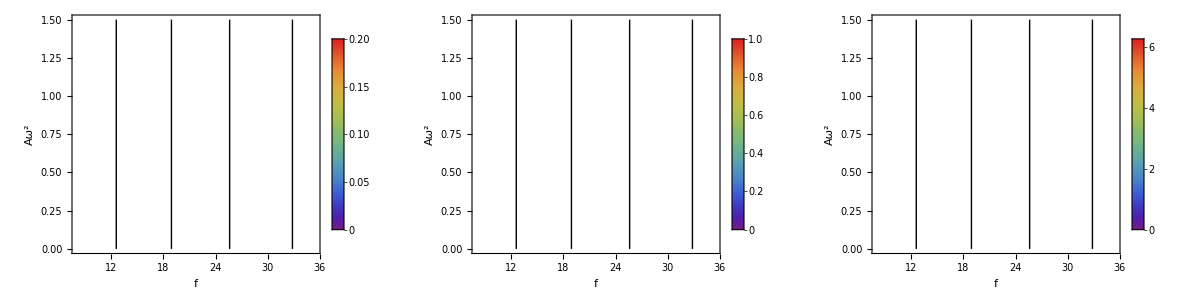

```mathematica
filebase="sweeps/randomacc"
growth1=Flatten[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1];
Amin=Min[growth1[[All,2]]];
Amax=Max[growth1[[All,2]]];
fmin=Min[growth1[[All,1]]];
fmax=Max[growth1[[All,1]]];
kmin=0;
kmax=2*Pi;
max=Max[growth1[[All,4]]];
ν1=0.5;
ν2=0;
ν3=0.1;
g=980;
σ=50;
length=3.5;
p1=Grid[{{Show[rasterizeBackground[Show[ListDensityPlot[growth1[[All,{1,2,4}]],InterpolationOrder->0,PlotRange->{All,All,{0.0,max}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Growth Rate"}},Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]}],Plot[2*(ν1+ν3*k^2+ν2*k*Tanh[k*height])*(1+σ/g*k^2)/(k*Tanh[k*height]*(g+σ*k^2))^(1/2)/.FindRoot[2*Pi*f/2==(k*Tanh[k*height]*(g+σ*k^2))^(1/2), {k,1.0}],{f,fmin,fmax},PlotStyle->Directive[Black]]]],Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},PlotRangeClipping->False,ImageSize->400,ImagePadding->{{65,100},{50,50}}],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,3}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{0.0,1.1}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/1.0]&),ColorFunctionScaling->False,FrameLabel->{{Aω^2,None},{f,"Frequency"}},ImageSize->300],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[growth1[[All,{1,2,5}]],Position[growth1[[All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,Amin},{#,Amax}}]&/@Cases[frequencies,u_/;u>fmin&&u<fmax]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
```

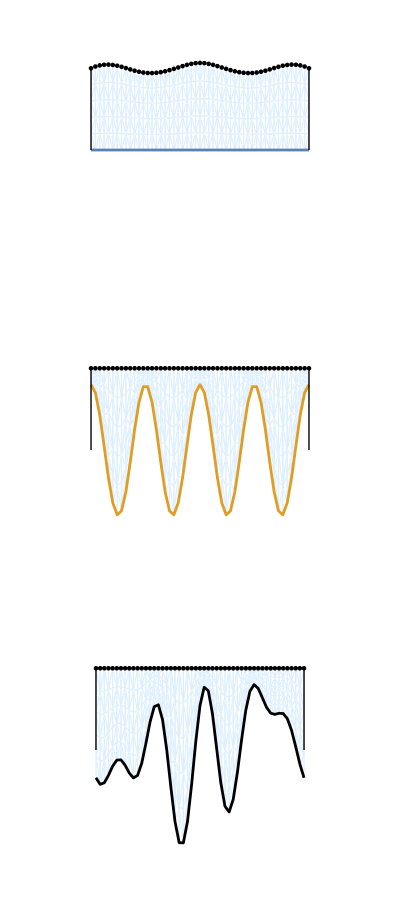

```mathematica
filebase="data/flat";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh]-100;
mesh2=mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];
filebase="data/periodic";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];
filebase="data/random";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
norms=BinaryReadList[filebase<>"norms.npy","Real64"][[1+(10+BinaryReadList[filebase<>"norms.npy","Integer16"][[5]])*8/64;;-1]];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
top2=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Interior surface points coordinates"][[1]]+1]]]];
length=ToExpression[lst[[FirstPosition[lst,"Length"][[1]]+1]]];
height=ToExpression[lst[[FirstPosition[lst,"Height"][[1]]+1]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
contop=Cases[con,u_/;Length[Intersection[top,u]]==2];
conbottom=Cases[con,u_/;Length[Intersection[bottom,u]]==2];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p3=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[Black,AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];

p0=Grid[{{p1},{p2},{p3}}]
```

```mathematica
Length[top]
```

101

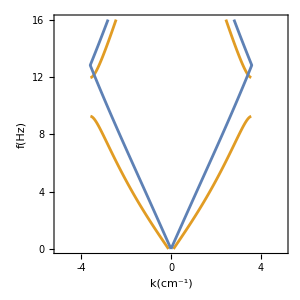
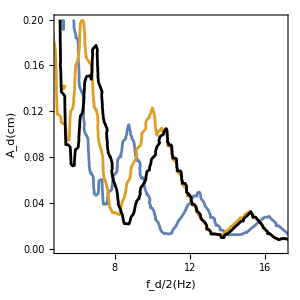
-Graphics- | -Graphics- | -Graphics-

plots/periodicrectanglegap.pdf

```mathematica
height=0.5;
length=3.5;
gap=2*Pi/length*4/2;
ks=2*gap;
hs=0.4;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν3=0.1;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-5,5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True]];
filebases={"sweeps/flat2amp","sweeps/periodic2amp","sweeps/random2amp"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],Black};p3=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{5,17},{0,0.2}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.2,0.04}],Table[{i,""},{i,0,0.2,0.04}]},{Table[{i,i},{i,4,16,2}],Table[{i,""},{i,4,16,2}]}}],{i,1,Length[sweeps]}];
p=Grid[{{p0,p1,p3}}]
Export["plots/periodicrectanglegap.pdf",p]
```

```mathematica
filebases={"sweeps/flat2acc","sweeps/periodic2acc","sweeps/random2acc"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Amin=Min[sweeps[[1,All,2]]];
Amax=Max[sweeps[[1,All,2]]];
fmin=Min[sweeps[[1,All,1]]];
fmax=Max[sweeps[[1,All,1]]];
kmin=Min[sweeps[[1,All,5]]];
kmax=Max[sweeps[[1,All,5]]];
max=Max[sweeps[[1,All,4]]];
p1=Table[rasterizeBackground[ListDensityPlot[{#[[1]],#[[2]],#[[3]]}&/@ReplacePart[sweeps[[i,All,{1,2,5}]],Position[sweeps[[i,All,{1,2,4}]],u_/;u<0]->-1],InterpolationOrder->0,PlotRange->{All,All,{kmin-0.01,kmax+0.01}},ClippingStyle->None,LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][(#-kmin)/(kmax-kmin)]&),ColorFunctionScaling->False, FrameLabel->{{Aω^2,None},{f,"Wave number"}},PlotRangeClipping->None,Prolog->{AbsoluteThickness[1],Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2,u_/;u>fmin&&u<fmax],Dashed,Line[{{1/2*#,Amin},{1/2*#,Amax}}]&/@Cases[frequencies2/2,u_/;u>fmin&&u<fmax&&u<Min[frequencies]*0.75]},Epilog->{Inset[BarLegend[{"Rainbow",{kmin,kmax}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],{i,1,Length[sweeps]}];
p=Grid[{p1}]
Export["plots/modes.pdf",p]
```

-Graphics- | -Graphics- | -Graphics-

plots/modes.pdf

Random substrates

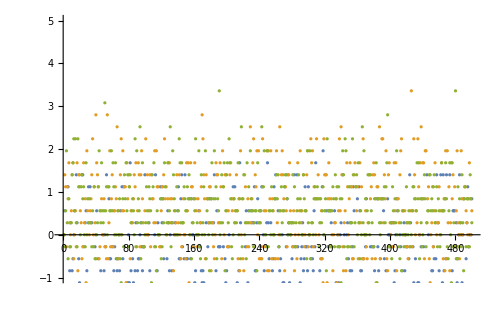

{480.,191.,51.,397.,218.,131.,94.,366.,243.,354.}

{426.,54.,170.,40.,229.,66.,438.,387.,340.,265.}

{229.,124.,299.,468.,142.,191.,131.,261.,244.,88.}

{4.2,3.36,6.44}

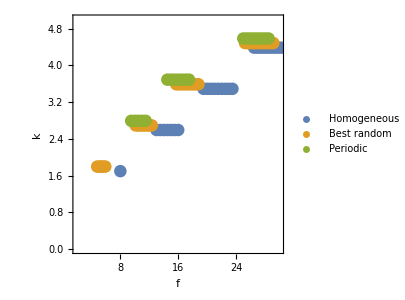

```mathematica
filebases={"sweeps/flat2acc","sweeps/periodic2acc"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,56}],1]&/@filebases;
filebase="sweeps/random";
random=DeleteCases[Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,500}],{}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6]&/@random)[[All,All,5]]]]];
means[case_]:=Mean/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(means/@wavenumbers[[2;;4]])-(means/@wavenumbers[[1;;3]]);
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[2;;-1]])-(maxes/@wavenumbers[[1;;-2]]);
shifts=Transpose[#-gaps[[All,1]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->{-1,5}]
DeleteCases[Reverse[SortBy[seeds,shifts[[3,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
DeleteCases[Reverse[SortBy[seeds,shifts[[2,First@FirstPosition[seeds,#]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
DeleteCases[Reverse[SortBy[seeds,Mean[shifts[[2;;3,First@FirstPosition[seeds,#]]]]&]],u_/;MemberQ[Position[gaps,Mean[{}]][[All,2]],Round[u]]][[1;;10]]
m=191;
gaps[[All,m]]
minind=First@FirstPosition[Abs[DeleteDuplicates[sweeps[[1,All,2]]]-First@DeleteDuplicates[Flatten[random[[All,All,2]]]]],Min[Abs[DeleteDuplicates[sweeps[[1,All,2]]]-First@DeleteDuplicates[Flatten[random[[All,All,2]]]]]]];
min=DeleteDuplicates[sweeps[[1,All,2]]][[minind]];
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[sweeps[[1]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[m]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[sweeps[[2]],u_/;u[[2]]==min&&u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{2,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Periodic"}]
```

Flat substrate Floquet predictions

```mathematica
rate[k_,ω_,A_,ν_]:=Module[{t0,t1,sol,norms,maxes},
t0=2*Pi*25;
t1=2*Pi*50;
sol=First@NDSolve[{ω^2*h''[t]==k*Tanh[k]*((-1+A*ω*Sin[t])*h[t]-ν*ω*h'[t]), h[0]==0.001, h'[0]==0}, h[t], {t,0,t1}];
norms=Table[h[t]/.sol,{t,t0,t1,2*Pi*0.1}];
maxes=First/@Position[Differences[Sign[Differences[norms]]],-2];
If[Mean[Log[Abs[norms]]]/Log[10]<-5,{k,ω,A,1/(0.1*Mean[Differences[maxes]]),-1,norms},{k,ω,A,1/(0.1*Mean[Differences[maxes]]),D[ω*Fit[Transpose[{2*Pi*0.1*maxes,Log[Abs[norms[[maxes]]]]}][[Ceiling[Length[maxes]/2];;-1]],{1,x},x],x],norms}]]
ωmin=1.5;
ωmax=3.0;
Amin=0.0;
Amax=0.3;
ν=0.05;
M=50;
AbsoluteTiming[Monitor[rates=Flatten[Table[First@MaximalBy[Table[rate[k,ω,A,ν][[1;;5]],{k,modes}],#[[5]]&],{ω,ωmin,ωmax,(ωmax-ωmin)/M},{A,Amin,Amax,(Amax-Amin)/M}],1];,N[{(ω-ωmin)/(ωmax-ωmin),(A-Amin)/(Amax-Amin)}]]]
```

{48.6212,Null}

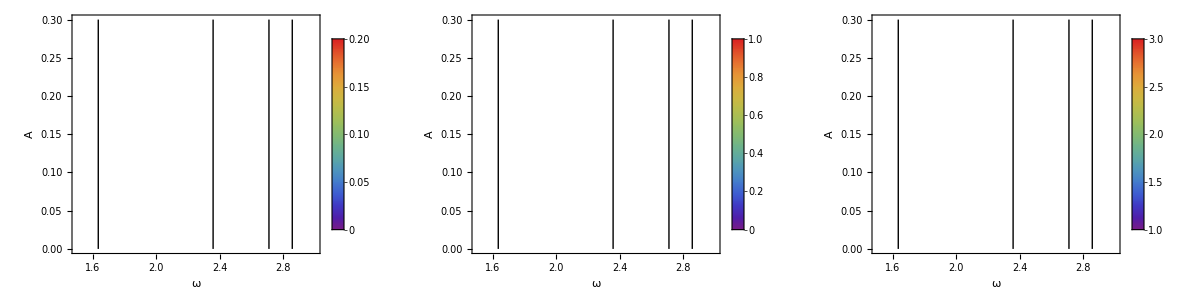

plots/benchmark.pdf

```mathematica
p2=Grid[{{rasterizeBackground[Show[ListDensityPlot[rates[[All,{2,3,5}]],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],PlotRange->{0,0.2},ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/0.2]&), FrameLabel->{{A,None},{ω,"Growth Rate"}},ClippingStyle->None],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,0.2}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,4}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][#/1]&),PlotRange->{0,1.1},ClippingStyle->None, FrameLabel->{{A,None},{ω,"Frequency"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{0,1}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]],rasterizeBackground[Show[ListDensityPlot[ReplacePart[rates[[All,{2,3,1}]],Position[rates[[All,{2,3,5}]],u_/;u<0]->-1],InterpolationOrder->0,ImageSize->300,LabelStyle->Directive[16,Black],ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][(#-1)/2]&),PlotRange->{0.9,3.1}, ClippingStyle->None,FrameLabel->{{A,None},{ω,"Wave Number"}}],PlotRangeClipping->None,Epilog->{Inset[BarLegend[{"Rainbow",{1,3}},LabelStyle->Directive[16,Black]],Scaled[{1.2,0.5}]],Line[{{#,0},{#,0.3}}]&/@Cases[(2*(modes*Tanh[modes])^(1/2)),u_/;u<3]},ImageSize->400,ImagePadding->{{65,100},{50,50}}]]}}]
p=Grid[{{p1},{p2}}];
Export["plots/benchmark.pdf",p]
```

Generate random narrow peaks

{0.,1.5708,3.14159,4.71239}

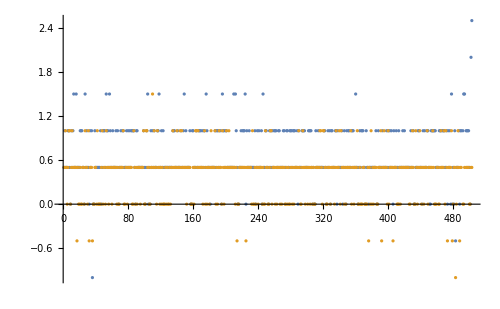

{495,491,503,502,494,493,478,360,246,224}

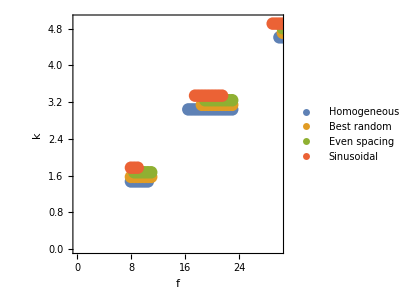

```mathematica
filebase="sweeps/sharp";
random=Table[If[FileExistsQ[filebase<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[filebase<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,503}];
seeds=Flatten[DeleteDuplicates/@random[[All,All,7]]];
wavenumbers=Sort[DeleteDuplicates[Flatten[(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6]&/@random)[[All,All,5]]]]]
mins[case_]:=Min/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
maxes[case_]:=Max/@(Cases[#,u_/;u[[4]]>0.0&&u[[3]]<0.6&&u[[5]]==case]&/@random)[[All,All,1]]
gaps=(mins/@wavenumbers[[3;;-1]])-(maxes/@wavenumbers[[2;;-2]]);
shifts=Transpose[#-gaps[[All,501]]&/@(Transpose[gaps])];
ListPlot[shifts,ImageSize->500,PlotRange->All]
Reverse[Ordering[shifts[[1]]]][[1;;10]]
m=494;
ListPlot[{{#[[1]],#[[2]]-0.1}&/@Cases[random[[501]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],Cases[random[[m]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.1}&/@Cases[random[[502]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]],{#[[1]],#[[2]]+0.2}&/@Cases[random[[503]],u_/;u[[4]]>0.0&&u[[3]]<0.6][[All,{1,5}]]},PlotRange->{{0,30},{0,5}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"f","k"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1,PlotStyle->Directive[PointSize[0.03]],PlotLegends->{"Homogeneous","Best random","Even spacing","Sinusoidal"}]
```

```mathematica
shifts[[1,478]]
shifts[[1,502]]
shifts[[1,503]]
```

1.5

2.

2.5

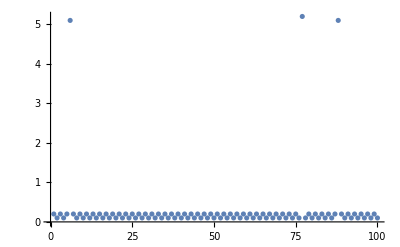

{71,11,18}

```mathematica
{{M},ssin,scos}=Import["sweeps/sharp/21/substrate.dat"];
h0=Table[Sum[ssin[[i]]*Sin[Pi*(i-1)*(j-1)/M]+scos[[i]]*Cos[Pi*(i-1)*(j-1)/M],{i,1,M}],{j,1,M}];
ListPlot[h0,PlotRange->All]
{#[[1]],#[[2]],100-#[[1]]-#[[2]]}&@Differences[First/@Position[h0,u_/;u>Mean[h0]*2]]
```

```mathematica
scos[[2]]
```

0.

```mathematica
gaps[[1,2]]
Position[gaps[[1,All]],∞]
Position[gaps[[1,All]],8.5]
Position[gaps[[1,All]],8.]
```

7.

{{4},{5},{6},{7},{11},{24},{25},{41},{50}}

{{1}}

{{3},{21},{58}}

```mathematica
8.5-7
8-7
1/1.5
```

1.5

1

0.666667

```mathematica
M=100;
num=3;
Monitor[Do[bottom=ConstantArray[0,M];
indices=RandomInteger[{2,M-1},num];
bottom[[indices]]=bottom[[indices]]+ConstantArray[1.0,num];
c=Re[Fourier[bottom]];
s=Im[Fourier[bottom]];
If[!DirectoryQ["data/sharp/"<>ToString[j]],CreateDirectory["data/sharp/"<>ToString[j]]];
file=OpenWrite["data/sharp/"<>ToString[j]<>"/substrate.dat"];
WriteLine[file,M];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[s,ConstantArray[0.,M]]}];
WriteLine[file,""];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[c,ConstantArray[0.,M]]}];
WriteLine[file,""];
Close[file];,{j,1,500}],j];
bottom=ConstantArray[0,M];
indices=Table[Round[i],{i,M/6,M,M/3}];
bottom[[indices]]=bottom[[indices]]+ConstantArray[1.0,3];
c=Re[Fourier[bottom]];
s=Im[Fourier[bottom]];
If[!DirectoryQ["data/sharp/"<>ToString[0]],CreateDirectory["data/sharp/"<>ToString[0]]];
file=OpenWrite["data/sharp/"<>ToString[0]<>"/substrate.dat"];
WriteLine[file,M];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[s,ConstantArray[0.,M]]}];
WriteLine[file,""];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[c,ConstantArray[0.,M]]}];
WriteLine[file,""];
Close[file];
If[!DirectoryQ["data/sharp/"<>ToString[-1]],CreateDirectory["data/sharp/"<>ToString[-1]]];
file=OpenWrite["data/sharp/"<>ToString[-1]<>"/substrate.dat"];
WriteLine[file,M];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[s,ConstantArray[0.,M]]}];
WriteLine[file,""];
Do[WriteString[file,ToString[i,FortranForm]<>" "],{i,Riffle[c,ConstantArray[0.,M]]}];
WriteLine[file,""];
Close[file];
```

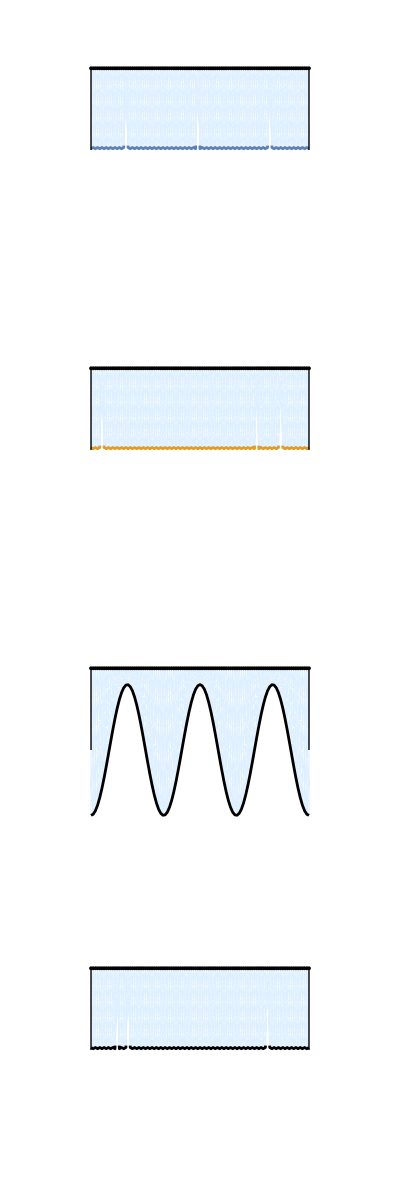

plots/sharpsubstrates.pdf

```mathematica
height=0.5;
length=4;
filebase="data/sharp0";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p1=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];
filebase="data/sharp21";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p2=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];
filebase="data/sharp-2";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p3=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[Black,AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];
filebase="data/sharp478";
lst=StringSplit[Import[filebase<>".txt"],"\n"];
meshpoints=ToExpression[lst[[FirstPosition[lst,"Mesh points"][[1]]+1]]];
mesh=Partition[Partition[BinaryReadList[filebase<>".npy","Real64"][[1+(10+BinaryReadList[filebase<>".npy","Integer16"][[5]])*8/64;;-1]],2],meshpoints];
top=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Surface points coordinates"][[1]]+1]]]];
bottom=1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Substrate points coordinates"][[1]]+1]]]];
con=Partition[1+ToExpression[StringSplit[lst[[FirstPosition[lst,"Mesh cells"][[1]]+1]]," "]],3];
sides=Flatten[Position[mesh[[-1]],u_/;Length[u]>0&&(Abs[(u[[1]]^2)^(1/2)-length]<10^-6||Abs[(u[[1]]^2)^(1/2)]<10^-6)]];
m=Length[mesh];
mesh2=mesh[[m]];
p4=Show[ListPlot[{mesh2[[top]]}, PlotStyle->Directive[Black], ImageSize->300,Axes->False,Frame->False,Prolog->{White,EdgeForm[LightBlue],Triangle[{mesh2[[#[[1]]]],mesh2[[#[[2]]]],mesh2[[#[[3]]]]}]&/@con},AspectRatio->(1.5)/(length+2),PlotRange->{{-1,length+1},{-0.75,0.75}}],ListPlot[mesh2[[bottom]],Joined->True,PlotStyle->{Directive[Black,AbsoluteThickness[2]]}],Epilog->{Opacity[1.0],Black,Line[{{0,0},{0,height}}],Line[{{length,0},{length,height}}]}];

p0=Grid[{{p1},{p2},{p3},{p4}}]
Export["plots/sharpsubstrates.pdf",p0]
```

Interpolation::indp: There are duplicated abscissa points in {{4.,0.},{4.,0.00370377},{4.,0.00740754},{4.,0.0111109},{4.,0.0148147},{4.,0.0185185},{4.,0.0222222},{4.,0.025926},{4.,0.0296294},«33»,{4.,0.155555},{4.,0.159259},{4.,0.162963},{4.,0.166666},{4.,0.17037},{4.,0.174074},{4.,0.177778},{4.,0.181481},«3030»}.

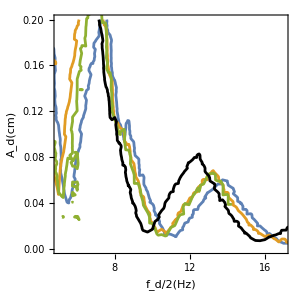

```mathematica
filebases={"sweeps/sharpamp/501","sweeps/sharpamp/502","sweeps/sharpamp/478","sweeps/sharpamp/503"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
interpolations[f_,a_]=Table[Interpolation[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],InterpolationOrder->1][f,a],{i,1,Length[sweeps]}];cols={ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]],ColorData[97,"ColorList"][[3]],Black};p3=Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.01},PlotRange->{{5,17},{0,0.2}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.2,0.04}],Table[{i,""},{i,0,0.2,0.04}]},{Table[{i,i},{i,4,16,2}],Table[{i,""},{i,4,16,2}]}}],{i,1,Length[sweeps]}]
```

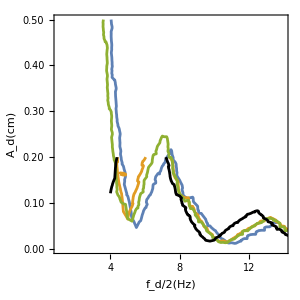

```mathematica
filebases={"sweeps/sharpamp/501","sweeps/sharpamp/502","sweeps/sharpamp/478","sweeps/sharpamp/503"};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.5},PlotRange->{{1,14},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black],ColorFunction->(ColorData["Rainbow"][#/max]&),ColorFunctionScaling->False, FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.2,0.04}]},{Table[{i,i},{i,4,16,2}],Table[{i,""},{i,4,16,2}]}}],{i,1,Length[sweeps]}]
```

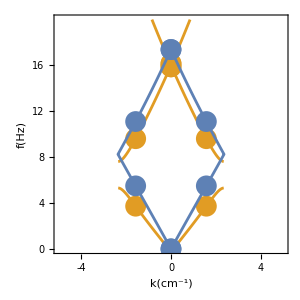

```mathematica
height=0.5;
length=4.0;
gap=2*Pi/length*3/2;
ks=2*gap;
hs=0.4;
M2=4;
κ[k_, n_]:=k+n*ks;
ν1=2;
ν3=0.1;
g=980;
σ=72;
ρ=1;
H1[k_,A_]:=Table[Exp[-κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])-Exp[κ[k,n]*height]*(g+σ/ρ*κ[k,n]^2)*κ[k,n]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H2[k_,A_]:=-Table[Exp[-κ[k,n]*height]*(BesselJ[m-n,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n-1,-I*κ[k,n]*A]-I/2*ks*A*BesselJ[m-n+1,-I*κ[k,n]*A])+Exp[κ[k,n]*height]*(BesselJ[m-n,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n-1,I*κ[k,n]*A]+I/2*ks*A*BesselJ[m-n+1,I*κ[k,n]*A]),{n,-M2,M2},{m,-M2,M2}];
H3[k_,A_]:=Table[1.0/Cosh[κ[k,n]*height]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2}];
sys[k_,A_]:={H3[k,A].H1[k,A],H3[k,A].H2[k,A]};
p1=Show[Show[ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,2*Pi/length,2*Pi/length}]],Joined->False,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-5,5},{0,20}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,20}},PlotStyle->Directive[PointSize[0.05],ColorData[97,"ColorList"][[2]]]],ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,-2*Pi/length,-2*Pi/length}]],Joined->False,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-5,5},{0,20}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[PointSize[0.05],ColorData[97,"ColorList"][[2]]]],ListPlot[Transpose[Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,-ks/2+0.01,ks/2-0.01,ks/200}]],Joined->True,Axes->False,Frame->True,LabelStyle->Directive[16],PlotRange->{{-5,5},{0,20}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,16}},PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]]],Show[ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,2*Pi/length}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,2*Pi/length}]},Joined->False,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.05]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,20}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True],ListPlot[{Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}],Table[{-If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,Pi/length/50}]},Joined->True,Axes->False,Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[2.0]],PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2.0]],AspectRatio->1,ImageSize->300,ImagePadding->{{65,10},{65,10}},LabelStyle->Directive[16],PlotRange->{{-2.5,2.5},{0,20}},FrameTicks->{{Table[{i,i},{i,0,16,4}],Table[{i,""},{i,4,14,2}]},{Table[{i,i},{i,-4,4,2}],Table[{i,""},{i,-4,4,2}]}},FrameLabel->{DisplayForm[RowBox[{k,"(",Superscript["cm",-1],")"}]],DisplayForm[RowBox[{f,"(Hz)"}]]},RotateLabel->True]]]
```

```mathematica
Table[{k,#^(1/2)/(2*Pi)-0.25}&/@SingularValueList[sys[k,hs]][[-3;;-1]],{k,0,2*Pi/length,2*Pi/length}]
Table[{If[k<gap,k,If[k<3*gap,2*gap-k,k-4*gap]],(g*k*Tanh[k*height]*(1+σ/g*k^2))^(1/2)/(2*Pi)},{k,0,6*Pi/length,2*Pi/length}]
```

{{{0.,41.5203},{0.,16.1656},{0.,15.8789}},{{1.5708,23.6468},{1.5708,9.61364},{1.5708,3.72751}}}

{{0.,0.},{1.5708,5.49608},{1.5708,11.108},{0.,17.3882}}

```mathematica
11.108047233251904-5.496079863487159
9.613643550531075-3.7275122296569463
```

5.61197

5.88613

```mathematica
17.388191789404228-11.108047233251904
15.878905310217917-9.613643550531075
```

6.28014

6.26526